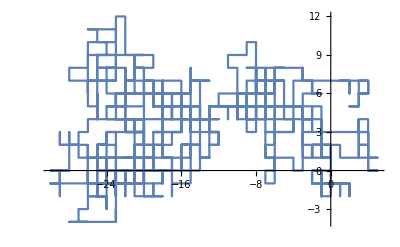

```mathematica
nn = 1000;
pointarray = ConstantArray[0,{nn,2}];
For[i=2,i≤nn,i++,
(
pointarray[[i]]=pointarray[[i-1]];
Switch[RandomInteger[3],
0,pointarray[[i,1]]=(pointarray[[i-1,1]]-1),
1,pointarray[[i,1]]=(pointarray[[i-1,1]]+1),
2,pointarray[[i,2]]=(pointarray[[i-1,2]]-1),
3,pointarray[[i,2]]=(pointarray[[i-1,2]]+1)
]
)
]
ListLinePlot[pointarray,PlotRange->All]
(*Manipulate[ListLinePlot[{pointarray[[;;n]]},PlotRange->{{-10,10},{-10,10}}],{n,1,nn,1}]*)
```

mh算法抽样高斯

```mathematica
(*目标分布*)
Πpdf[x_]:=PDF[NormalDistribution[0.5,0.2],x];
(*建议分布*)
gpdf[x_]:=PDF[UniformDistribution[{0,1}],x];
(*建议分布抽样*)
markovx= RandomVariate[UniformDistribution[{0,1}],1000];
(*计算单个状态的一步转移*)
onestatetrans[i_]:=(
u = RandomReal[{0,1}];
y=RandomReal[{0,1}];
If[u<=Πpdf[y]/Πpdf[markovx[[i]]],markovx[[i]]=y,markovx[[i]]=markovx[[i]]]
)
```

15.427147

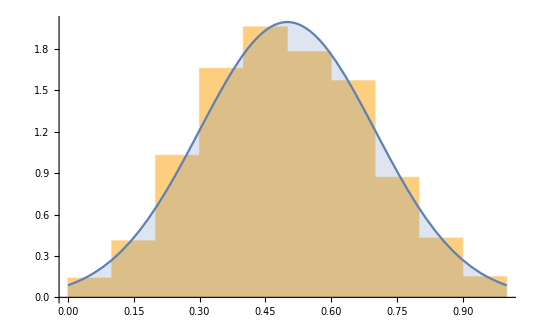

```mathematica
start = AbsoluteTime[];
For[n=1,n≤50,n++,
markovx=ParallelTable[onestatetrans[i],{i,1,Length[markovx],1}];
]
end = AbsoluteTime[];
Print[end-start]
Show[{
Histogram[markovx,10,"PDF"],
Plot[Πpdf[x],{x,0,1},Filling->Axis,Exclusions->None]
}]
```

```mathematica
markovx = RandomVariate[UniformDistribution[{0,1}]];
start = AbsoluteTime[];
For[n=1,n≤50,n++,
(
u = RandomReal[{0,1}];
y=RandomReal[{0,1}];
If[u<=Πpdf[y]/Πpdf[markovx],markovx=y,markovx=markovx]
)
]
simplex = ConstantArray[0,1000];
For[n=1,n≤Length[simplex],n++,
(
u = RandomReal[{0,1}];
y=RandomReal[{0,1}];
If[u<=Πpdf[y]/Πpdf[markovx],markovx=y,markovx=markovx];
simplex[[n]]=markovx
)
]
end = AbsoluteTime[];
Print[end-start]
```

0.278139

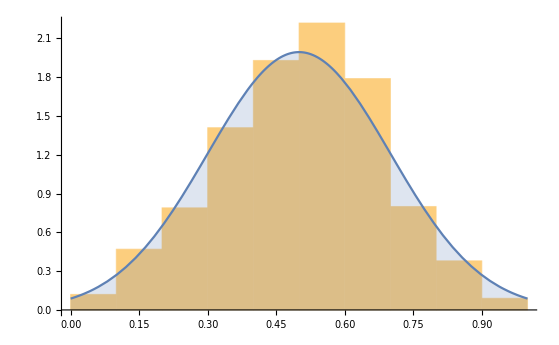

```mathematica
Show[{
Histogram[simplex,10,"PDF"],
Plot[Πpdf[x],{x,0,1},Filling->Axis,Exclusions->None]
}]
```

```mathematica
AbsoluteTime[]
```

3.8706200791782328×10^9